```mathematica
ψ[a_,b_,x_,y_]:=2/L Sin[(a π)/L(x-L/2)]Sin[(b π)/L(y-L/2)]
```

```mathematica
ψM[x_,y_]:=(ψ[5,7,x,y]-ψ[7,5,x,y])/(√2)
```

```mathematica
L=1;
```

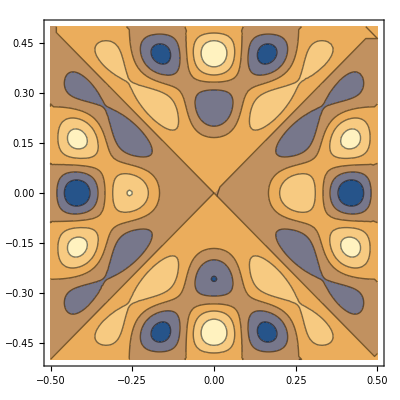

```mathematica
ContourPlot[ψM[x,y],{x,-.5,.5},{y,-.5,.5}]
```